## Matrix Element calculation (including time evolution)

```mathematica
Clear[m,hbar,ω,ωt,t,n]
```

```mathematica
hbar = 1.0545718×10^-34;m = 6.94 * 1.660539 10^-27 ; ω = 10^6;ωt=4*10^7; t = 10^-7; n = 2;
```

```mathematica
Integrate[Integrate[1/Sqrt[2^n  n!]((m ω)/(Pi hbar))^(1/4) Exp[(-m ω x^2)/(2 hbar)] *HermiteH[n,Sqrt[(m ω)/hbar]x] 1/Sqrt[2^(n+2)  (n+2)!]((m ω)/(Pi hbar))^(1/4) Exp[(-m ω x^2)/(2 hbar)] *HermiteH[n+2,Sqrt[(m ω)/hbar]x]*((m ω)/(2 Pi ⅈ hbar Sin[ω t]))^(1/2) Exp[ⅈ/(2 hbar Sin[ω t])((x^2+ xt^2)Cos[ω t]-2 x xt)],{xt, -1, 1}],{x,-1,1}]
```

```mathematica
Series[1/Sqrt[2^n  n!]((m ω)/(Pi hbar))^(1/4) Exp[(-m ω x^2)/(2 hbar)] *HermiteH[n,Sqrt[(m ω)/hbar]x] 1/Sqrt[2^(n+2)  (n+2)!]((m ω)/(Pi hbar))^(1/4) Exp[(-m ω x^2)/(2 hbar)] *HermiteH[n+2,Sqrt[(m ω)/hbar]x]*((m ω)/(2 Pi ⅈ hbar Sin[ω t]))^(1/2) Exp[ⅈ/(2 hbar Sin[ωt t])((x^2+ xt^2)Cos[ωt t]-2 x xt)],{ω,0,1}]//FullSimplify
```

(2^(1/2+2 n) ⅇ^((ⅈ (-2 x xt+(x^2+xt^2) Cos[t ωt]) Csc[t ωt])/(2 hbar)) √(m/hbar) √(-(ⅈ m)/(hbar t)) √ω)/(Gamma[-1/2-n/2] Gamma[1/2-n/2] √(2^n Gamma[1+n]) √(2^n Gamma[3+n]))-(ⅈ ⅇ^((ⅈ (-2 x xt+(x^2+xt^2) Cos[t ωt]) Csc[t ωt])/(2 hbar)) (3+2 n) (-(ⅈ m)/(hbar t))^(3/2) t x √(2^n Gamma[1+n]) Sin[n π] ω)/(π^(3/2) √(2^(1+n) Gamma[3+n]))+O[ω]^(3/2)

```mathematica
nmax = 15;η = 0.25; τ = 27.102 10^-9;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 6.94 * 1.660539 10^-27 ;
```

```mathematica
Dr[n,nt]= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η 1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η 1)^2]Exp[-η^2/2];
Drw[n,nt,,θ]= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  Cos[θ])^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  Cos[θ])^2]Exp[-(η  Cos[θ])^2/2];
ψ[n_, ω_, x_]:= 1/Sqrt[2^n  n!]((m ω)/(Pi hbar))^(1/4) Exp[(-m ω x^2)/(2 hbar)] *HermiteH[n,Sqrt[(m ω)/hbar]x]; (*Wikipedia*)
CustomDelta[x_] := Piecewise[{{1, x ==0}, {0, x ≠0}}]
(*UP[ω_,x_,xt_,t_]:= ((m ω)/(2 Pi ⅈ hbar Sin[ω t]))^(1/2) Exp[ⅈ/(2 hbar Sin[ω t])((x^2+ xt^2)Cos[ω t]-2 x xt)];*)
U[ω_, ωt_,n_, nt_, t_]:= CustomDelta[nt-n-2] Sqrt[(n+1)(n+2)]/4(Max[{ω, ωt}]^2-Min[{ω, ωt}]^2)/Max[{ω, ωt}] t+ CustomDelta[nt-n+2] Sqrt[(n - 2+1)(n - 2+2)]/4(Max[{ω, ωt}]^2-Min[{ω, ωt}]^2)/Max[{ω, ωt}] t + CustomDelta[n-nt]*Sqrt[((1- Sqrt[(n+1)(n+2)]/4(Max[{ω, ωt}]^2-Min[{ω, ωt}]^2)/Max[{ω, ωt}] t)^2 - (Sqrt[(n - 2+1)(n - 2+2)]/4(Max[{ω, ωt}]^2-Min[{ω, ωt}]^2)/Max[{ω, ωt}] t)^2)]
CustomDelta[x_] := Piecewise[{{1, x ==0}, {0, x ≠0}}]
M[n_,nt_] :=NIntegrate[Sin[θ]/2 Abs[Sum[√((Min[n,m]!)/((Min[n,m]+Abs[m-n])!))(ⅈ η Cos[θ] )^Abs[m-n] LaguerreL[Min[n,m],Abs[m-n],(η Cos[θ])^2]Exp[-(η Cos[θ])^2/2] Dr[m,nt],{m,0,nmax}]]^2,{θ,0, Pi}]
```

```mathematica
Umat = Table[U[1*10^5, 2*10^5, n, nt, 10^-7],{n,0,nmax},{nt,0,nmax}]//N
```

{{0.994697,0.,0.0053033,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.990814,0.,0.00918559,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.0053033,0.,0.986995,0.,0.0129904,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.00918559,0.,0.983187,0.,0.0167705,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.0129904,0.,0.979374,0.,0.0205396,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.0167705,0.,0.975553,0.,0.0243028,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.0205396,0.,0.971721,0.,0.0280624,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.0243028,0.,0.967875,0.,0.0318198,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.0280624,0.,0.964016,0.,0.0355756,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.0318198,0.,0.960143,0.,0.0393303,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.0355756,0.,0.956254,0.,0.0430842,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0393303,0.,0.952351,0.,0.0468375,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0430842,0.,0.948432,0.,0.0505903,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0468375,0.,0.944497,0.,0.0543427},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0505903,0.,0.940546,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0543427,0.,0.936578}}

```mathematica
Decay Paths
```

```mathematica
omegas = 
gammas =
```

```mathematica
UA[n,nt] = UDr[n,nt]
```

```mathematica
Dr[1,1]
```

0.940991+0. ⅈ

```mathematica
M [3,3]
```

0.708382

```mathematica
DrMat = Table[Dr[n,nt],{n,0,nmax },{nt,0,nmax}] ;
```

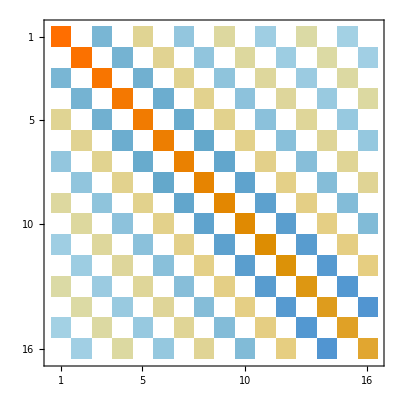

```mathematica
MatrixPlot[DrMat]
```

```mathematica
Table[ Sum[Abs[DrMat[[j,m]]]^2,{m,1,11}],{j,1,16}]
```

{1.,1.,1.,1.,1.,1.,1.,0.999969,0.998516,0.964967,0.680377,0.313077,0.0405458,0.00245716,0.0000887457,2.17738×10^-6}

```mathematica
Mat = Table[M[n,nt],{n,0,nmax},{nt,0,nmax}]
```

{{0.949132,0.0484942+0. ⅈ,0.00228486,0.0000861472+0. ⅈ,2.66257×10^-6,6.93947×10^-8+0. ⅈ,1.56062×10^-9,3.08366×10^-11+0. ⅈ,5.43085×10^-13,8.62454×10^-15+0. ⅈ,1.24683×10^-16,1.65401×10^-18+0. ⅈ,2.02698×10^-20,2.30804×10^-22+0. ⅈ,2.45409×10^-24,2.44727×10^-26+0. ⅈ},{0.0484942+0. ⅈ,0.856714,0.0881073+0. ⅈ,0.00634836,0.000323635+0. ⅈ,0.0000126283,3.97857×10^-7+0. ⅈ,1.0497×10^-8,2.38081×10^-10+0. ⅈ,4.73377×10^-12,8.37699×10^-14+0. ⅈ,1.33537×10^-15,1.93647×10^-17+0. ⅈ,2.57541×10^-19,3.16291×10^-21+0. ⅈ,3.60809×10^-23},{0.00228486,0.0881073+0. ⅈ,0.776986,0.120068+0. ⅈ,0.0117561,0.000759734+0. ⅈ,0.0000359315,1.33045×10^-6+0. ⅈ,4.03424×10^-8,1.03391×10^-9+0. ⅈ,2.29222×10^-11,4.47496×10^-13+0. ⅈ,7.80088×10^-15,1.22802×10^-16+0. ⅈ,1.76194×10^-18,2.32199×10^-20+0. ⅈ},{0.0000861472+0. ⅈ,0.00634836,0.120068+0. ⅈ,0.708383,0.145467+0. ⅈ,0.0181374,0.00142649+0. ⅈ,0.0000795059,3.38945×10^-6+0. ⅈ,1.16276×10^-7,3.3257×10^-9+0. ⅈ,8.13934×10^-11,1.7385×10^-12+0. ⅈ,3.29113×10^-14,5.59094×10^-16+0. ⅈ,8.61003×10^-18},{2.66257×10^-6,0.000323635+0. ⅈ,0.0117561,0.145467+0. ⅈ,0.649504,0.165266+0. ⅈ,0.0251786,0.00234313+0. ⅈ,0.00015077,7.28497×10^-6+0. ⅈ,2.79256×10^-7,8.82499×10^-9+0. ⅈ,2.36458×10^-10,5.48743×10^-12+0. ⅈ,1.12145×10^-13,2.04546×10^-15+0. ⅈ},{6.93947×10^-8+0. ⅈ,0.0000126283+0. ⅈ,0.000759734+0. ⅈ,0.0181374+0. ⅈ,0.165266+0. ⅈ,0.599102+0. ⅈ,0.180316+0. ⅈ,0.0326158+0. ⅈ,0.00351817+0. ⅈ,0.000257281+0. ⅈ,0.0000139165+0. ⅈ,5.90155×10^-7+0. ⅈ,2.04362×10^-8+0. ⅈ,5.95324×10^-10+0. ⅈ,1.49218×10^-11+0. ⅈ,3.27555×10^-13+0. ⅈ},{1.56062×10^-9+0. ⅈ,3.97857×10^-7+0. ⅈ,0.0000359315+0. ⅈ,0.00142649+0. ⅈ,0.0251786+0. ⅈ,0.180316+0. ⅈ,0.556067+0. ⅈ,0.191363+0. ⅈ,0.0402299+0. ⅈ,0.00495134+0. ⅈ,0.000406456+0. ⅈ,0.0000243668+0. ⅈ,1.13372×10^-6+0. ⅈ,4.27211×10^-8+0. ⅈ,1.34504×10^-9+0. ⅈ,3.62326×10^-11+0. ⅈ},{3.08366×10^-11+0. ⅈ,1.0497×10^-8+0. ⅈ,1.33045×10^-6+0. ⅈ,0.0000795059+0. ⅈ,0.00234313+0. ⅈ,0.0326158+0. ⅈ,0.191363+0. ⅈ,0.519412+0. ⅈ,0.199062+0. ⅈ,0.0478403+0. ⅈ,0.00663519+0. ⅈ,0.000605345+0. ⅈ,0.0000398899+0. ⅈ,2.02222×10^-6+0. ⅈ,8.24309×10^-8+0. ⅈ,2.7915×10^-9+0. ⅈ},{5.43085×10^-13+0. ⅈ,2.38081×10^-10+0. ⅈ,4.03424×10^-8+0. ⅈ,3.38945×10^-6+0. ⅈ,0.00015077+0. ⅈ,0.00351817+0. ⅈ,0.0402299+0. ⅈ,0.199062+0. ⅈ,0.488266+0. ⅈ,0.203986+0. ⅈ,0.0553007+0. ⅈ,0.00855655+0. ⅈ,0.00086045+0. ⅈ,0.0000618949+0. ⅈ,3.39849×10^-6+0. ⅈ,1.49199×10^-7+0. ⅈ},{8.62454×10^-15+0. ⅈ,4.73377×10^-12+0. ⅈ,1.03391×10^-9+0. ⅈ,1.16276×10^-7+0. ⅈ,7.28497×10^-6+0. ⅈ,0.000257281+0. ⅈ,0.00495134+0. ⅈ,0.0478403+0. ⅈ,0.203986+0. ⅈ,0.461856+0. ⅈ,0.206634+0. ⅈ,0.0624945+0. ⅈ,0.0106978+0. ⅈ,0.0011776+0. ⅈ,0.0000919109+0. ⅈ,5.44724×10^-6+0. ⅈ},{1.24683×10^-16+0. ⅈ,8.37699×10^-14+0. ⅈ,2.29222×10^-11+0. ⅈ,3.3257×10^-9+0. ⅈ,2.79256×10^-7+0. ⅈ,0.0000139165+0. ⅈ,0.000406456+0. ⅈ,0.00663519+0. ⅈ,0.0553007+0. ⅈ,0.206634+0. ⅈ,0.439503+0. ⅈ,0.207436+0. ⅈ,0.069331+0. ⅈ,0.0130385+0. ⅈ,0.00156118+0. ⅈ,0.000132066+0. ⅈ},{1.65401×10^-18+0. ⅈ,1.33537×10^-15+0. ⅈ,4.47496×10^-13+0. ⅈ,8.13934×10^-11+0. ⅈ,8.82499×10^-9+0. ⅈ,5.90155×10^-7+0. ⅈ,0.0000243668+0. ⅈ,0.000605345+0. ⅈ,0.00855655+0. ⅈ,0.0624945+0. ⅈ,0.207436+0. ⅈ,0.420607+0. ⅈ,0.206764+0. ⅈ,0.0757511+0. ⅈ,0.015536+0. ⅈ,0.00203329+0. ⅈ},{2.02698×10^-20+0. ⅈ,1.93647×10^-17+0. ⅈ,7.80088×10^-15+0. ⅈ,1.7385×10^-12+0. ⅈ,2.36458×10^-10+0. ⅈ,2.04362×10^-8+0. ⅈ,1.13372×10^-6+0. ⅈ,0.0000398899+0. ⅈ,0.00086045+0. ⅈ,0.0106978+0. ⅈ,0.069331+0. ⅈ,0.206763+0. ⅈ,0.404618+0. ⅈ,0.205039+0. ⅈ,0.0813855+0. ⅈ,0.0185853+0. ⅈ},{2.30804×10^-22+0. ⅈ,2.57541×10^-19+0. ⅈ,1.22802×10^-16+0. ⅈ,3.29113×10^-14+0. ⅈ,5.48743×10^-12+0. ⅈ,5.95324×10^-10+0. ⅈ,4.27211×10^-8+0. ⅈ,2.02222×10^-6+0. ⅈ,0.000061895+0. ⅈ,0.00117761+0. ⅈ,0.0130388+0. ⅈ,0.0757552+0. ⅈ,0.20501+0. ⅈ,0.389891+0. ⅈ,0.20113+0. ⅈ,0.0914117+0. ⅈ},{2.45409×10^-24+0. ⅈ,3.16291×10^-21+0. ⅈ,1.76194×10^-18+0. ⅈ,5.59093×10^-16+0. ⅈ,1.12145×10^-13+0. ⅈ,1.49218×10^-11+0. ⅈ,1.34502×10^-9+0. ⅈ,8.24286×10^-8+0. ⅈ,3.39826×10^-6+0. ⅈ,0.0000918957+0. ⅈ,0.00156053+0. ⅈ,0.0155196+0. ⅈ,0.0811648+0. ⅈ,0.1985+0. ⅈ,0.360054+0. ⅈ,0.234713+0. ⅈ},{2.44727×10^-26+0. ⅈ,3.6081×10^-23+0. ⅈ,2.32201×10^-20+0. ⅈ,8.61021×10^-18+0. ⅈ,2.04555×10^-15+0. ⅈ,3.27588×10^-13+0. ⅈ,3.62404×10^-11+0. ⅈ,2.79282×10^-9+0. ⅈ,1.49356×10^-7+0. ⅈ,5.45997×10^-6+0. ⅈ,0.000132759+0. ⅈ,0.00205717+0. ⅈ,0.0190555+0. ⅈ,0.0957962+0. ⅈ,0.222114+0. ⅈ,0.209847+0. ⅈ}}

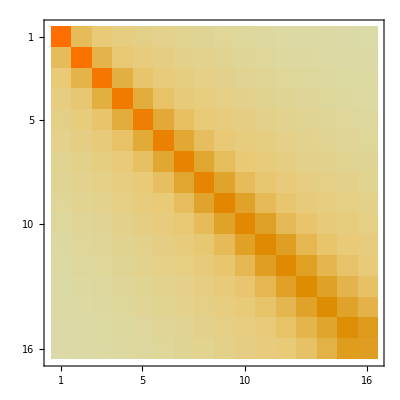

```mathematica
MatrixPlot[Mat]
```

```mathematica
<
```

```mathematica
Table[ Sum[Mat[[j,m]],{m,1,11}],{j,1,16}]
```

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.999999+0. ⅈ,0.999974+0. ⅈ,0.999353+0. ⅈ,0.990518+0. ⅈ,0.925532+0. ⅈ,0.708493+0. ⅈ,0.279117+0. ⅈ,0.0809303+0. ⅈ,0.0142804+0. ⅈ,0.00165591+0. ⅈ,0.000138371+0. ⅈ}

```mathematica
{0.9500066076371911+0. ⅈ,0.9981858353884894+0. ⅈ,0.9999252554603134+0. ⅈ,0.9999975389684228+0. ⅈ,0.9999999137599004+0. ⅈ,0.9999989443099998+0. ⅈ,0.9999639056062806+0. ⅈ,0.9991850718498525+0. ⅈ,0.9869398839062721+0. ⅈ,0.8466419397926749+0. ⅈ,0.11540074126484189+0. ⅈ}
Table[ Sum[M[j,m],{m,1,40}],{j,1,40}]
```

{0.950007+0. ⅈ,0.998186+0. ⅈ,0.999925+0. ⅈ,0.999998+0. ⅈ,1.+0. ⅈ,0.999999+0. ⅈ,0.999964+0. ⅈ,0.999185+0. ⅈ,0.98694+0. ⅈ,0.846642+0. ⅈ,0.115401+0. ⅈ}

{0.980684,0.999521,0.999992,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999999,0.999894,0.993787,0.84998,0.149262,0.00692783,0.000149055,1.88655×10^-6,1.59863×10^-8,9.83276×10^-11,4.63835×10^-13,1.74623×10^-15,5.40682×10^-18,1.40948×10^-20,3.15211×10^-23,6.1407×10^-26,1.05545×10^-28,1.61778×10^-31,2.23173×10^-34,2.79275×10^-37,3.1921×10^-40,3.3527×10^-43,3.25314×10^-46,2.92995×10^-49,2.45986×10^-52,1.93247×10^-55,1.42548×10^-58,9.90425×10^-62}

```mathematica
Adiabatic elimination of state 2
```

```mathematica
α = 0.6;
```

```mathematica
Eigenvalues[Mat]
```

{0.976214,0.897995,0.77029,0.605649,0.4216,-0.396012,-0.386373,-0.342232,-0.329749,-0.238988,0.234944,-0.227032,0.114543,-0.102563,-0.0745253,0.0575847}

```mathematica
MatEl2 = Mat.Inverse[IdentityMatrix[nmax+1]-(1-α)*Mat]
```

{{1.53376+0. ⅈ,0.119664+0. ⅈ,0.011568+0. ⅈ,0.00141105+0. ⅈ,0.000214689+0. ⅈ,0.0000384659+0. ⅈ,7.80744×10^-6+0. ⅈ,1.75271×10^-6+0. ⅈ,4.27811×10^-7+0. ⅈ,1.12096×10^-7+0. ⅈ,3.12233×10^-8+0. ⅈ,9.17406×10^-9+0. ⅈ,2.82546×10^-9+0. ⅈ,9.06342×10^-10+0. ⅈ,2.97959×10^-10+0. ⅈ,9.98857×10^-11+0. ⅈ},{0.119664+0. ⅈ,1.31757+0. ⅈ,0.197289+0. ⅈ,0.0270965+0. ⅈ,0.00411901+0. ⅈ,0.000735629+0. ⅈ,0.000149375+0. ⅈ,0.0000335367+0. ⅈ,8.18554×10^-6+0. ⅈ,2.1448×10^-6+0. ⅈ,5.97413×10^-7+0. ⅈ,1.75532×10^-7+0. ⅈ,5.40611×10^-8+0. ⅈ,1.73415×10^-8+0. ⅈ,5.70101×10^-9+0. ⅈ,1.91117×10^-9+0. ⅈ},{0.011568+0. ⅈ,0.197289+0. ⅈ,1.15514+0. ⅈ,0.249273+0. ⅈ,0.0435677+0. ⅈ,0.00778391+0. ⅈ,0.00157349+0. ⅈ,0.000353458+0. ⅈ,0.0000862857+0. ⅈ,0.0000226076+0. ⅈ,6.2971×10^-6+0. ⅈ,1.85023×10^-6+0. ⅈ,5.69839×10^-7+0. ⅈ,1.82791×10^-7+0. ⅈ,6.00924×10^-8+0. ⅈ,2.0145×10^-8+0. ⅈ},{0.00141105+0. ⅈ,0.0270965+0. ⅈ,0.249273+0. ⅈ,1.02898+0. ⅈ,0.284501+0. ⅈ,0.0597015+0. ⅈ,0.012097+0. ⅈ,0.00270102+0. ⅈ,0.000659778+0. ⅈ,0.000172916+0. ⅈ,0.0000481599+0. ⅈ,0.0000141503+0. ⅈ,4.3581×10^-6+0. ⅈ,1.39798×10^-6+0. ⅈ,4.59583×10^-7+0. ⅈ,1.54068×10^-7+0. ⅈ},{0.000214689+0. ⅈ,0.00411901+0. ⅈ,0.0435677+0. ⅈ,0.284501+0. ⅈ,0.928685+0. ⅈ,0.308232+0. ⅈ,0.0749534+0. ⅈ,0.0168222+0. ⅈ,0.00407693+0. ⅈ,0.0010692+0. ⅈ,0.00029792+0. ⅈ,0.0000875251+0. ⅈ,0.0000269559+0. ⅈ,8.64694×10^-6+0. ⅈ,2.84267×10^-6+0. ⅈ,9.52957×10^-7+0. ⅈ},{0.0000384659+0. ⅈ,0.000735629+0. ⅈ,0.00778391+0. ⅈ,0.0597015+0. ⅈ,0.308232+0. ⅈ,0.847575+0. ⅈ,0.323789+0. ⅈ,0.0891104+0. ⅈ,0.0217891+0. ⅈ,0.00565759+0. ⅈ,0.00157742+0. ⅈ,0.000463727+0. ⅈ,0.000142799+0. ⅈ,0.0000458053+0. ⅈ,0.0000150587+0. ⅈ,5.04818×10^-6+0. ⅈ},{7.80744×10^-6+0. ⅈ,0.000149375+0. ⅈ,0.00157349+0. ⅈ,0.012097+0. ⅈ,0.0749534+0. ⅈ,0.323789+0. ⅈ,0.781146+0. ⅈ,0.333381+0. ⅈ,0.102114+0. ⅈ,0.0268783+0. ⅈ,0.00740219+0. ⅈ,0.00217713+0. ⅈ,0.000671046+0. ⅈ,0.000215215+0. ⅈ,0.0000707481+0. ⅈ,0.0000237177+0. ⅈ},{1.75271×10^-6+0. ⅈ,0.0000335367+0. ⅈ,0.000353458+0. ⅈ,0.00270102+0. ⅈ,0.0168222+0. ⅈ,0.0891104+0. ⅈ,0.333381+0. ⅈ,0.726216+0. ⅈ,0.338537+0. ⅈ,0.113976+0. ⅈ,0.032007+0. ⅈ,0.0092747+0. ⅈ,0.00285918+0. ⅈ,0.000918171+0. ⅈ,0.000301778+0. ⅈ,0.000101158+0. ⅈ},{4.27811×10^-7+0. ⅈ,8.18554×10^-6+0. ⅈ,0.0000862857+0. ⅈ,0.000659778+0. ⅈ,0.00407693+0. ⅈ,0.0217891+0. ⅈ,0.102114+0. ⅈ,0.338537+0. ⅈ,0.680455+0. ⅈ,0.340357+0. ⅈ,0.12474+0. ⅈ,0.0371188+0. ⅈ,0.0112431+0. ⅈ,0.00360923+0. ⅈ,0.00118832+0. ⅈ,0.000398258+0. ⅈ},{1.12096×10^-7+0. ⅈ,2.1448×10^-6+0. ⅈ,0.0000226076+0. ⅈ,0.000172916+0. ⅈ,0.0010692+0. ⅈ,0.00565759+0. ⅈ,0.0268783+0. ⅈ,0.113976+0. ⅈ,0.340357+0. ⅈ,0.642108+0. ⅈ,0.339651+0. ⅈ,0.134461+0. ⅈ,0.0421701+0. ⅈ,0.0132639+0. ⅈ,0.004362+0. ⅈ,0.00146517+0. ⅈ},{3.12233×10^-8+0. ⅈ,5.97413×10^-7+0. ⅈ,6.2971×10^-6+0. ⅈ,0.0000481599+0. ⅈ,0.00029792+0. ⅈ,0.00157742+0. ⅈ,0.00740219+0. ⅈ,0.032007+0. ⅈ,0.12474+0. ⅈ,0.339651+0. ⅈ,0.609819+0. ⅈ,0.337029+0. ⅈ,0.143177+0. ⅈ,0.0470737+0. ⅈ,0.0151263+0. ⅈ,0.00507051+0. ⅈ},{9.17406×10^-9+0. ⅈ,1.75532×10^-7+0. ⅈ,1.85023×10^-6+0. ⅈ,0.0000141503+0. ⅈ,0.0000875251+0. ⅈ,0.000463727+0. ⅈ,0.00217713+0. ⅈ,0.0092747+0. ⅈ,0.0371188+0. ⅈ,0.134461+0. ⅈ,0.337029+0. ⅈ,0.582496+0. ⅈ,0.332906+0. ⅈ,0.150741+0. ⅈ,0.0511951+0. ⅈ,0.0167219+0. ⅈ},{2.82546×10^-9+0. ⅈ,5.4061×10^-8+0. ⅈ,5.69839×10^-7+0. ⅈ,4.35809×10^-6+0. ⅈ,0.0000269559+0. ⅈ,0.000142799+0. ⅈ,0.000671046+0. ⅈ,0.00285918+0. ⅈ,0.011243+0. ⅈ,0.0421701+0. ⅈ,0.143177+0. ⅈ,0.332905+0. ⅈ,0.559072+0. ⅈ,0.327168+0. ⅈ,0.155229+0. ⅈ,0.0540973+0. ⅈ},{9.06442×10^-10+0. ⅈ,1.73435×10^-8+0. ⅈ,1.82811×10^-7+0. ⅈ,1.39813×10^-6+0. ⅈ,8.6479×10^-6+0. ⅈ,0.0000458103+0. ⅈ,0.000215239+0. ⅈ,0.000918273+0. ⅈ,0.00360963+0. ⅈ,0.0132654+0. ⅈ,0.0470787+0. ⅈ,0.150763+0. ⅈ,0.327189+0. ⅈ,0.536178+0. ⅈ,0.315159+0. ⅈ,0.156281+0. ⅈ},{2.97147×10^-10+0. ⅈ,5.68549×10^-9+0. ⅈ,5.99287×10^-8+0. ⅈ,4.58331×10^-7+0. ⅈ,2.83493×10^-6+0. ⅈ,0.0000150177+0. ⅈ,0.0000705555+0. ⅈ,0.000300957+0. ⅈ,0.00118509+0. ⅈ,0.0043501+0. ⅈ,0.0150845+0. ⅈ,0.0510627+0. ⅈ,0.15487+0. ⅈ,0.312741+0. ⅈ,0.489533+0. ⅈ,0.320177+0. ⅈ},{1.00593×10^-10+0. ⅈ,1.92471×10^-9+0. ⅈ,2.02877×10^-8+0. ⅈ,1.55159×10^-7+0. ⅈ,9.59707×10^-7+0. ⅈ,5.08394×10^-6+0. ⅈ,0.0000238858+0. ⅈ,0.000101874+0. ⅈ,0.00040107+0. ⅈ,0.00147565+0. ⅈ,0.00510743+0. ⅈ,0.0168175+0. ⅈ,0.0544674+0. ⅈ,0.160194+0. ⅈ,0.304466+0. ⅈ,0.26713+0. ⅈ}}

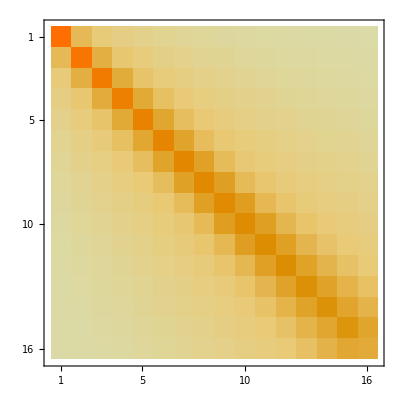

```mathematica
MatrixPlot[MatEl2]
```

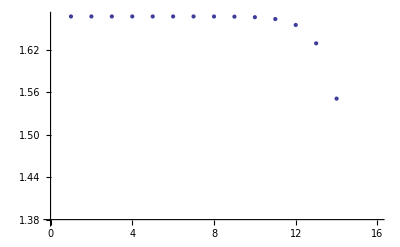

```mathematica
ListPlot[Table[ Sum[MatEl2 [[j,m]],{m,1,16}],{j,1,16}]]
```